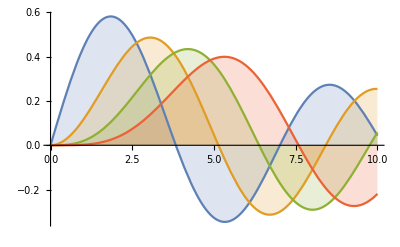
-Graphics-Grid[BesselFunction,Frame→True]

```mathematica
ClearAll["Global`*"];
Panel[Row[{Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling-> Axis],Grid[Style["BesselFunction",FontFamily->"Felix Titling"],Frame->True]}]]
```

```mathematica
Grid[Text["BesselFunction"],Frame->True]
```

Grid[BesselFunction,Frame→True]

```mathematica
Grid[Text["BesselFunction"],Frame->All]
```

Grid[BesselFunction,Frame→All]

```mathematica
Row[Text["BesselFunction"],Frame->All]
```

Row[BesselFunction,Frame→All]

```mathematica
Grid[{Text["BesselFunction"],{}},Frame->All]
```

Grid[{BesselFunction,{}},Frame→All]

```mathematica
Grid[{"BesselFunction",{}},Frame->All]
```

Grid[{BesselFunction,{}},Frame→All]

```mathematica
Grid[{{"BesselFunction"},{"Introduction"}},Frame->All,Alignment-> Left]
```

BesselFunction
Introduction

```mathematica
Grid[{{Grid[{{"BesselFunction"},{"Introduction"}},Alignment-> Left]}},Frame->All]
```

BesselFunction
Introduction

```mathematica
Grid[{{Text["BesselFunction"]}},Frame->All]
```

BesselFunction

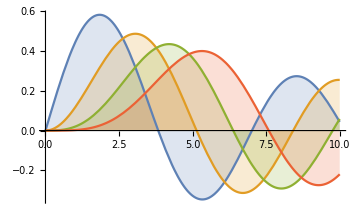
-Graphics-BesselFunction

```mathematica
Grid[{{Row[{Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling-> Axis,ImageSize->Medium],Grid[{{Style["BesselFunction",FontFamily->"Felix Titling"]}},Frame->All]}]}},Frame->All]
```

```mathematica
Manipulate[DynamicModule[{f},Column[{Slider[Dynamic[f],{1,10,1}],Plot[waveFunction[Dynamic[f],x],{x,-2π,2π},PlotRange->Automatic,ImageSize->Large]}]],Initialization:> (waveFunction[f_,x_]:=Cos[f*x]+Sin[f*x])]
```

```mathematica
DynamicModule[{red=0,green=0,blue=0},Column[{Grid[{{Graphics[{Red,Rectangle[]},ImageSize->30],Slider[Dynamic[red]]},{Graphics[{Green,Rectangle[]},ImageSize->30],Slider[Dynamic[green]]},{Graphics[{Blue,Rectangle[]},ImageSize->30],Slider[Dynamic[blue]]}}],Dynamic[Graphics[{RGBColor[Dynamic[red],Dynamic[green],Dynamic[blue]],Disk[]}]]}]]
```

ReplaceAll::reps: {
GraphicsBox[{},
AspectRatio->NCache[GoldenRatio^(-1), 0.6180339887498948],
Axes->{True, True},
AxesLabel->{None, None},
AxesOrigin->{0, 0},
DisplayFunction->Identity,
Frame->{{False, False}, {False, False}},
FrameLabel->{{None, None}, {None, None}},
FrameTicks->{{Automatic, Automatic}, {Automatic, Automatic}},
GridLines->{None, None},
GridLinesStyle->Directive[
GrayLevel[0.5, 0.4]],
ImageSize->Large,
Method->{"DefaultBoundaryStyle" -> Automatic, "DefaultMeshStyle" -> AbsolutePointSize[6], "ScalingFunctions" -> None},
PlotRange->{{0., 0.}, {0., 0.}},
PlotRangeClipping->True,
PlotRangePadding->{{
Scaled[0.02], 
Scaled[0.02]}, {
Scaled[0.05], 
Scaled[0.05]}},
Ticks->{Automatic, Automatic}], BaseStyle → {}, DefaultBaseStyle → {}, Deinitialization :> None, DynamicModuleParent → None, DynamicModuleValues → Automatic, InheritScope → False, Initialization :> None, SaveDefinitions → False, SynchronousInitialization → True, UndoTrackedVariables :> None, UnsavedVariables :> None, UntrackedVariables :> None} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/ReplaceAll/reps",
ButtonNote->"ReplaceAll::reps"]

```mathematica
Manipulate[DynamicModule[{f=1},Grid[{{Slider[Dynamic[f]],Dynamic@Plot[thisfunc[f,x],{f,1,10},PlotRange->Automatic,ImageSize-> Large]}}]],{x,-2π,2π}]
```

```mathematica
Manipulate[Plot[thisfunc[x,f],{x,-2π,2π},PlotRange->Automatic,ImageSize->Large],{{f,1,"frequency"},1,50,ControlType-> Slider}]
```

```mathematica
Manipulate[Grid[{{Plot[thisfunc[x,f],{x,-50,50},PlotRange->Automatic,ColorFunction->"Rainbow",ImageSize->Large]},{Grid[{{Switch[text,1,Style[" Long Radio Wave\n This is the Long Radio Wave\n It's wave length is between 10^2 to 10^8 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],2,Style[" Short Radio Wave\n This is the Short Radio Wave\n It's wave length is between 1 to 10^2 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],3,Style[" Microwave\n This is the Microwave\n It's wave length is between 10^-3 to 1 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],4,Style[" IR\n This the IR wave\n It's wave length is between 10^-6 to 10^-3 meters.",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],5,Style[" Visible Spectrum\n These are waves that is visible to human eyes.\n It's wave length is between 10^-7 to 10^-6 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],6,Style[" UV\n This is the UV wave\n It's wave length is around 10^-7 mters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],7,Style[" EUV\n This is EUV wave.\ It's wave length is around 10^-8 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],8,Style[" SX\n This is Soft X-ray\n It's wave length is around 10^-9 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],9,Style[" HX\n This is Hard X-ray\n It's wave length is around 10^-10 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20],10,Style[" γ\n This is γ wave\n It's wave length is around 10^-12 meters",FontFamily-> "Arial",RGBColor[0.32,0.42,0.65],FontSize->20]]}},Frame->All,Alignment->Top,Background-> Pink]}}],{{f,1,"frequency"},1,10,1,ControlType-> Slider},{{text,1,"content"},1,10,1,ControlType-> Slider},Initialization:>(thisfunc[f_,x_]:= Cos[f*x]+Sin[f*x]),SaveDefinitions->True]
```